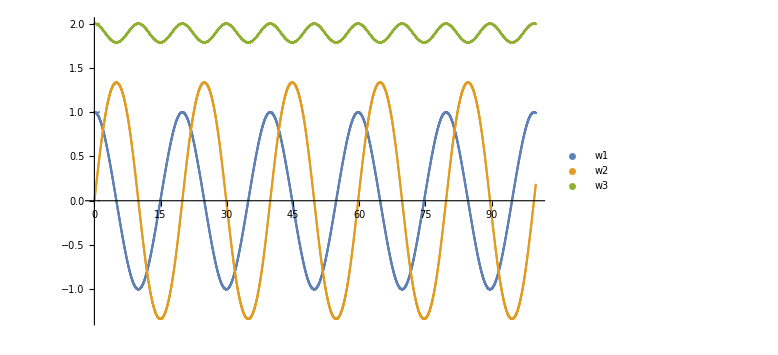

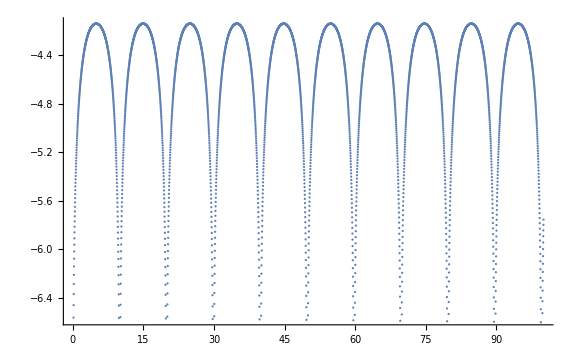

```mathematica
Clear["Global`*"]
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
I1=0.8;
I2=0.9;
I3=1;
dtvalue=0.02;
imax=5000;
t=Table[i,{i,1,imax+1}];
w1=Table[i,{i,1,imax+1}];
w2=Table[i,{i,1,imax+1}];
w3=Table[i,{i,1,imax+1}];
w1[[1]]=1;
w2[[1]]=0;
w3[[1]]=2;
M1zer=I1*w1[[1]];
M2zer=I2*w2[[1]];
M3zer=I3*w3[[1]];
M51={M1zer,M2zer,M3zer};
Rx[u_]:={{1,0,0},{0,Cos[u],Sin[u]},{0,-Sin[u],Cos[u]}}
Ry[u_]:={{Cos[u],0,-Sin[u]},{0,1,0},{Sin[u],0,Cos[u]}}
Rz[u_]:={{Cos[u],Sin[u],0},{-Sin[u],Cos[u],0},{0,0,1}}
PhiHM1[t_,w1_,M_]:=Rx[w1*t/I1].M;
PhiHM2[t_,w2_,M_]:=Ry[w2*t/I2].M;
PhiHM3[t_,w3_,M_]:=Rz[w3*t/I3].M;
(*LoopStartinHere*)
Do[M11=PhiHM1[dtvalue/2,M51[[1]],M51];
M22=PhiHM2[dtvalue/2,M11[[2]],M11];
M33=PhiHM3[dtvalue,M22[[3]],M22];
M42=PhiHM2[dtvalue/2,M33[[2]],M33];
M51=PhiHM1[dtvalue/2,M42[[1]],M42];
w1[[i+1]]=M51[[1]]/I1;
w2[[i+1]]=M51[[2]]/I2;
w3[[i+1]]=M51[[3]]/I3;
t[[i+1]]=i*dtvalue;,{i,1,imax}]
w1data=Table[{t[[i]],w1[[i]]},{i,1,imax+1}];
w2data=Table[{t[[i]],w2[[i]]},{i,1,imax+1}];
w3data=Table[{t[[i]],w3[[i]]},{i,1,imax+1}];

Energy[w1_,w2_,w3_]:=(I1*w1^2+I2*w2^2+I3*w3^2)/2;
InitEnergy=Energy[w1[[1]],w2[[1]],w3[[1]]];
RltError[w1_,w2_,w3_]:=Log10[Abs[((Energy[w1,w2,w3]-InitEnergy)/InitEnergy)]];
error=Table[{t[[i]],RltError[w1[[i]],w2[[i]],w3[[i]]]},{i,1,imax+1}];
ListPlot[{w1data,w2data,w3data}, PlotLegends->{"w1","w2", "w3"},ImageSize->Large,PerformanceGoal->"Quality"]
ListPlot[error, ImageSize->Large,PerformanceGoal->"Quality"]
```

```mathematica
(*w1,w2,w3 functions appear to be identical to those provided by the analytical solution.
The error is periodic over time with constant amplitude, but it's worse when compared to the analytical solution and RK4 method.
However, if we had a longer final time tmax, the results could change.
To calculate a tmax at which the error of RK4 method is greater, we have to assume that the error from RK4 method increases at a rate of 10^(-1) for every t=100. To reach the levels of splitting method it would take 5*t, with an error of 10^(-4).
It's also worth mentioning that because our functions are periodic, their local maxima and minima occur at the same time. It appears to have an effect on our error as well.
w2 has its critical points (either maxima or minima) happen at the same time with w3 minima. At the same time, the error appears to be the local maximum.
w1 has its critical points (either maxima or minima) happen at the same time with w3 maxima. At the same time, the error appears to be the local minimum.
*)
```